# Neural Logic

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

```mathematica
?neurallogic`*
```

## Utilities

```mathematica
HardPrediction[m_]:=Ordering[(With[{t=#[True]},If[MissingQ[t],0,t]]&)/@Counts/@m,-1]
HardTarget[t_]:=Flatten[Position[t,True]]
HardResults[hardPredictionTargetPairs_]:=Module[{results,accuracy},
results=Reverse[Sort[Counts[{HardPrediction[First[#]][[1]],HardTarget[Last[#]][[1]]}&/@hardPredictionTargetPairs]]];
accuracy=KeySelect[results,First[#]==Last[#]&];
{"Accuracy = "<>ToString[Total[accuracy]/Length[hardPredictionTargetPairs]*100.0]<>"%",results}
]
```

```mathematica
HardPrediction[{{True,False,False},{False,False,False},{True,True,False}}]
```

{3}

```mathematica
HardPrediction[{{True,False,False},{True,False,False},{False,False,False}}]
```

{2}

```mathematica
HardPrediction[{{True,True,False},{True,False,False},{True,True,True}}]
```

Null

## Learn XOR

## Null

```mathematica
Null
```

Null

## Null

### Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

### Null

```mathematica
Null
```

```mathematica
Null
```

Null

### Null

```mathematica
Null
```

Null

Null

### Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

## Learn MNIST

## Generate training data

```mathematica
ConvertBinaryStringToList[s_String]:=ToExpression["{"<>StringInsert[s,",",Drop[Range[StringLength[s]],1]]<>"}"]
ConvertBinaryStringToImageData[s_String,{width_,height_}]:=ArrayReshape[ConvertBinaryStringToList[s],{width,height}]
MNISTExample[example_]:=(Soften/@ConvertBinaryStringToList[First[example]])->Last[example]
MNISTImageExample[example_,w_,h_]:=Image[ConvertBinaryStringToImageData[First[example],{w,h}],ImageSize->Tiny]->Last[example]
TargetClass[class_,numClasses_]:=Table[If[i==ToExpression[class]+1,1,0],{i,1,numClasses}]
```

```mathematica
first2Digits=12665;
first4Digits=24754;
data=Flatten[StringSplit/@Take[Import[FileNameJoin[{NotebookDirectory[],"data/mnist_data.csv"}]],first4Digits],1];
numClasses=Length[DeleteDuplicates[Last/@data]];
data=Map[First[#]->TargetClass[Last[#],numClasses]&,data];
```

```mathematica
MNISTImageExample[#,8,8]&/@RandomSample[data,8]
```

{-Graphics-→{1,0,0,0},-Graphics-→{0,1,0,0},-Graphics-→{1,0,0,0},-Graphics-→{0,1,0,0},-Graphics-→{0,0,0,1},-Graphics-→{0,1,0,0},-Graphics-→{0,1,0,0},-Graphics-→{1,0,0,0}}

```mathematica
{trainData,testData}=[MNISTExample/@data,"TestSetSize"->Scaled[0.8],"Shuffle"->True];
```

## Standard neural net

```mathematica
ConvertDataToClasses[data_]:=MapAt[First[Flatten[Position[#,1]]]-1&,data,{All,2}]
```

### Create net

```mathematica
net=With[{classificationLayerSize=numClasses},
NetChain[{
300,LogisticSigmoid,
classificationLayerSize,LogisticSigmoid,
SoftmaxLayer[]
},
"Output"->NetDecoder[{"Class",{"0","1","2","3"}}]
]];
```

### Train net

```mathematica
result=NetTrain[net,ConvertDataToClasses[trainData],All,
ValidationSet->{ConvertDataToClasses[RandomSample[testData,UpTo[1000]]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->2000];
```

### Evaluate net

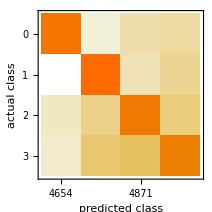
Classifier Measurements
Classifier method | Net
Number of test examples | 19803
Accuracy | (94.110.17) %
Accuracy baseline | (27.140.32) %
Geometric mean of probabilities | 0.448 ± 0.00065
Mean cross entropy | 0.802 ± 0.0014
Single evaluation time | 2.59 ms/example
Batch evaluation speed | 144. examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]
```

## Hard neural logic

### Create net

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=1024*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,50],
HardNeuralNAND[50,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=With[{classificationLayerSize=12*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,200],
HardNeuralMajority[200,classificationLayerSize],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{net,hardNet}=Block[{portSize,classificationLayerSize},
portSize=900;
classificationLayerSize=portSize*numClasses;
HardNeuralChain[
{
HardNeuralNAND[inputSize,classificationLayerSize],
HardDropoutLayer[0.5],
HardNeuralPortLayer[classificationLayerSize,numClasses]
}
]
];
```

```mathematica
softNet=NetGraph[<|"NeuralLogicNet"->net,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"}];
```

```mathematica
softNet
```

NetGraph[<>]

### Train net

```mathematica
result=NetTrain[softNet,trainData,All,
ValidationSet->{RandomSample[testData,UpTo[1000]],"Interval"->10},
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->4000];
```

```mathematica
trainedSoftNet=NetExtract[result["TrainedNet"],"NeuralLogicNet"]
```

NetChain[<>]

### Evaluate soft net

```mathematica
(*ClassifierMeasurements[result["TrainedNet"],ConvertDataToClasses[testData]]*)
```

```mathematica
softPredictionTargetPairs=[{trainedSoftNet[First[#]],Last[#]}&,testData];
hardenedPredictionTargetPairs=Harden[softPredictionTargetPairs];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 93.9858%
<|{2,2}→5167,{1,1}→4643,{4,4}→4410,{3,3}→4392,{3,4}→213,{2,4}→199,{4,3}→174,{2,3}→133,{4,2}→105,{1,3}→100,{1,4}→75,{3,2}→69,{4,1}→50,{3,1}→42,{2,1}→21,{1,2}→10|>

```mathematica
MatrixForm/@Flatten[RandomSample[hardenedPredictionTargetPairs,5],1]/.{True->Style[True,Red]};
```

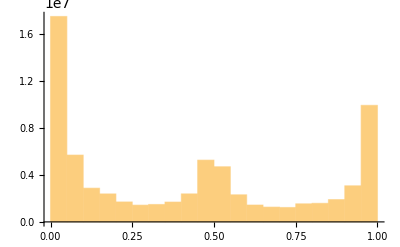

```mathematica
Histogram[Flatten[First/@softPredictionTargetPairs],PlotRange->All]
```

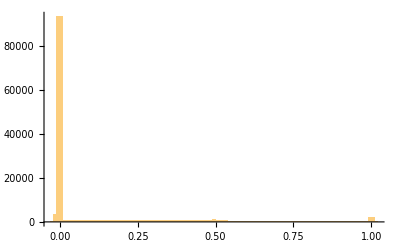

```mathematica
Histogram[Flatten[ExtractWeights[trainedSoftNet]],PlotRange->All]
```

### Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedSoftNet];
hardPredictionTargetPairs=[{hnf[Harden[First[#]]],Last[#]}&,testData];
Column[HardResults[hardenedPredictionTargetPairs]]
```

Accuracy = 93.9858%
<|{2,2}→5167,{1,1}→4643,{4,4}→4410,{3,3}→4392,{3,4}→213,{2,4}→199,{4,3}→174,{2,3}→133,{4,2}→105,{1,3}→100,{1,4}→75,{3,2}→69,{4,1}→50,{3,1}→42,{2,1}→21,{1,2}→10|>

```mathematica
SpaceSaving[trainedSoftNet]
```

Soft net size = 936. kilobytes
Hard net size = 29.25 kilobytes
Saving factor = 32.

## Approximate neural logic

### Null

```mathematica
Null
```

```mathematica
Null
```

### Null

```mathematica
Null
```

### Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

## Notes

```mathematica
Get["neural-logic.m",Path->NotebookDirectory[]];
```

## Counting

```mathematica
(* Experimental *)
net=With[{classificationLayerSize=32*numClasses},
NetGraph[
<|
"Layer1"->HardNeuralNAND[inputSize,600][[1]],
"Layer2"->HardNeuralNAND[600,classificationLayerSize][[1]],
"ToMatrix"->ReshapeLayer[{1,classificationLayerSize}],
"Require"->Require[HardNeuralLTEK[1,classificationLayerSize,32][[1]]][[1]],
"ToVector"->ReshapeLayer[{classificationLayerSize}],
"ClassPredictions"->HardNeuralPortLayer[classificationLayerSize,numClasses][[1]]
|>,
{
"Layer1"->"Layer2",
"Layer2"->"ToMatrix",
"ToMatrix"->"Require",
"Require"->"ToVector",
"ToVector"->"ClassPredictions"
}
]]
```